```mathematica
Quit
```

Kerr EOM

```mathematica
RPoly[r_,z_]:=( (ϵ(r^2+a^2)-a*L)^2-Δ[r](r^2+(a*ϵ-L)^2+Q))

ZPoly[r_, z_]:=(Q- z^2(a^2(1-ϵ^2)(1-z^2)+L^2+Q))

Polyϕ[r_,z_]:= (a/Δ[r](ϵ(r^2+a^2)-a L) + L/(1-z^2)-a ϵ)
TPoly[r_,z_]:=  ((r^2+a^2)/Δ[r](ϵ(r^2+a^2)-a L)-a^2 ϵ(1-z^2)+a L)
```

Dyonic EOM

```mathematica
Q  = 𝒞 - (L - a ϵ)^2;
Pt =( Qc r - a Pc z)/m;
PTt =( -Pc r - a Qc z)/m;
Pϕ = (Pc z (a^2+r^2)- a Qc r (1-z^2))/m;
PTϕ =( Qc z (a^2+r^2) + a Pc r (1-z^2))/m;
𝒫t = (e Pt - g PTt)/(r^2+a^2 z^2);
𝒫ϕ = (e Pϕ- g PTϕ)/(r^2+a^2 z^2);
ϵ= ℰ-𝒫t;
L = ℒ +𝒫ϕ;
```

```mathematica
Δ[r_] = r^2-2 r +a^2+ Qc^2+ Pc^2
```

a^2+Pc^2+Qc^2-2 r+r^2

```mathematica
𝒫ϕdel = (a^2 Ω  z+Ω r^2 z+a δ r (-1+z^2))/(m (r^2+a^2 z^2))
```

```mathematica
𝒫tdel = (δ r-a Ω z)/(m r^2+a^2 m z^2)
```

Put in 𝒫ϕ[r,z] and 𝒫t[r,z] terms explicitly

```mathematica
RPoly[r_]:=((g Pc r+e Qc r-m (a^2 ℰ+r^2 ℰ-a ℒ))^2)/m^2-(r^2+𝒞) Δ[r];
ZPoly[ z_]:=z^2 (-(e Pc-g Qc)^2/m^2-𝒞)+𝒞-a^2 (-1+z^2) (-ℰ^2+z^2 (-1+ℰ^2))+(2 (-e Pc+g Qc) z ℒ)/m-ℒ^2-(2 a (-1+z^2) ℰ (e Pc z-g Qc z+m ℒ))/m;

Polyϕ[r_,z_]:=(e Pc z-g Qc z+m (a (-1+z^2) ℰ+ℒ))/(m(1-z^2))+(a (-g Pc r-e Qc r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ[r]) ;
TPoly[r_,z_]:=((a^2+r^2) (-g Pc r-e Qc r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ[r])+ (a(e Pc z-g Qc z+m (a (-1+z^2) ℰ+ℒ)))/m;
```

where here (dr/dλ)^2 = RPoly[r_,z_],    (dz/dλ)^2 = ZPoly[r_,z_],  dϕ/dλ = ZPoly[r_,z_], dt/dλ = TPoly[r_,z_]

Now change back to 𝒬 param

```mathematica
RPoly[r_]:=((δ  r-m (a^2+r^2) ℰ+a m ℒ)^2)/m^2-(r^2+(-a ℰ+ℒ)^2+𝒦) Δ[r];
ZPoly[ z_]:=𝒦-z^2 𝒦-z 1/m^2(Ω^2 z+2 a m Ω (-1+z^2) ℰ+a^2 m^2 z (-1+z^2) (-1+ℰ^2)+2 m Ω ℒ+m^2 z ℒ^2);

Polyϕ[r_,z_]:=(Ω z+m (a (-1+z^2) ℰ+ℒ))/(m(1-z^2))+(a (-δ  r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ[r]) ;
TPoly[r_,z_]:=((a^2+r^2) (-δ r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ[r])+ (a(Ω z+m (a (-1+z^2) ℰ+ℒ)))/m;
```

### a = 0, L=0

```mathematica
Quit
```

```mathematica
RPoly[r_]:=((𝒩r-m r^2 ℰ)^2)/m^2-(r^2+𝒦) Δ[r];
ZPoly[ z_]:=𝒦-z^2( 𝒦+1/m^2 𝒮^2 );

Polyϕ[r_,z_]:=(𝒮 z)/(m(1-z^2)) ;
TPoly[r_,z_]:=(r^2 (-𝒩 r+m r^2 ℰ))/(m Δ[r]);
```

## Enery and Stuff

```mathematica
Pt =( Qc r - a Pc z)/m;
PTt =( -Pc r - a Qc z)/m;
Pϕ = (Pc z (a^2+r^2)- a Qc r (1-z^2))/m;
PTϕ =( Qc z (a^2+r^2) + a Pc r (1-z^2))/m;
𝒫t = (δ r-a Ω z)/(m r^2+a^2 m z^2);
𝒫ϕ = (a^2 Ω z+Ω r^2 z+a δ  r (-1+z^2))/(m (r^2+a^2 z^2));
```

### ErgoRegion Dionic BHs

```mathematica
Simplify[(r-M+Sqrt[M^2-a^2])(r-M-Sqrt[M^2-a^2])]
```

a^2+r (-2 M+r)

```mathematica
Quit[]
```

```mathematica
Simplify[-(Δ-a^2(1-z^2))Ut- a (1-z^2)(r^2+a^2-Δ)Uϕ - ((δ r-a Ω z)/(m r^2+a^2 m z^2))]
```

-a^2 Ut (-1+z^2)+a Uϕ (-1+z^2) (a^2+r^2-Δ)-Ut Δ+(-r δ+a z Ω)/(m (r^2+a^2 z^2))

```mathematica
Solve[r^2+a^2 (Cos^2)[θ]+𝒬^2- 2 M r==0, r]
```

{{r→M-√(M^2-𝒬^2-a^2 Cos^2[θ])},{r→M+√(M^2-𝒬^2-a^2 Cos^2[θ])}}

```mathematica
Simplify[(a^2-r (+r)+a^2 (Sin^2)[θ])/(r^2+a^2 (Cos^2)[θ])]
```

(a^2-r^2+a^2 Sin^2[θ])/(r^2+a^2 Cos^2[θ])

0.01

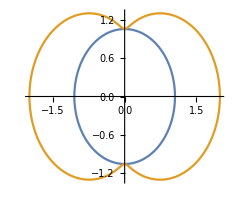

```mathematica
M =1;
a = 0.99;
eps = 0.01
𝒬 = Sqrt[1-a^2]-eps;
PolarPlot[{M + Sqrt[M^2-a^2-𝒬^2], M + Sqrt[M^2-a^2(Cos[θ-π/2])^2-𝒬^2]}, {θ,-π,π}]
```

```mathematica
(a^2 Ω  z+Ω r^2 z+a δ r (-1+z^2))/(m (r^2+a^2 z^2))
```

```mathematica
(δ r-a Ω z)/(m r^2+a^2 m z^2)
```

### Energy Extraction

```mathematica
Energy = -(KtU  + (a Ω)/(m r^2+a^2 m z^2) z);
Angular  = (KϕU - (a^2 + r^2)/(m (r^2+a^2 z^2))Ωz);
```

```mathematica
Quit[]
```

```mathematica
Simplify[(2 a^2 r^2+r^4+a^4 (Cos^2)[θ]+a^2 (2 M r-r^2-𝒬^2) (Sin^2)[θ])/(r^2+a^2(Cos^2)[θ])]
```

```mathematica
Simplify[(2 a^2 r^2+r^4+a^4 (Cos^2)[θ]+a^2 (2 M r-r^2-𝒬^2) (1-(Cos^2)[θ]))/(r^2+a^2 (Cos^2)[θ])]
```

(r^4+a^2 (2 M r+r^2-𝒬^2)+a^2 (a^2-2 M r+r^2+𝒬^2) Cos^2[θ])/(r^2+a^2 Cos^2[θ])

```mathematica
Ω=0.9;
m=1;
r= M + Sqrt[M^2-a^2(Cos[θ-π/2])^2-𝒬^2]
```

1+√(0.982821-0.9801 Sin[θ]^2)

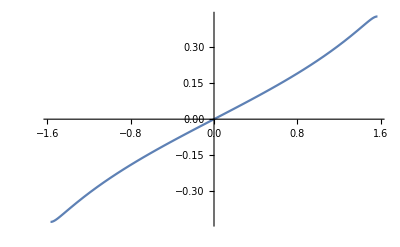

```mathematica
Plot[ (a Ω)/(m r^2+a^2 m Cos[θ-π/2]^2) Cos[θ-π/2], {θ, -π/2,π/2}]
```

### Writing extra term in vector

```mathematica
Quit[]
```

```mathematica
Uz[z_]:= 𝒦-z^2 𝒦-z 1/m^2(Ω^2 z+2 a m Ω (-1+z^2) ℰ+a^2 m^2 z (-1+z^2) (-1+ℰ^2)+2 m Ω ℒ+m^2 z ℒ^2)
```

4

0.001

1

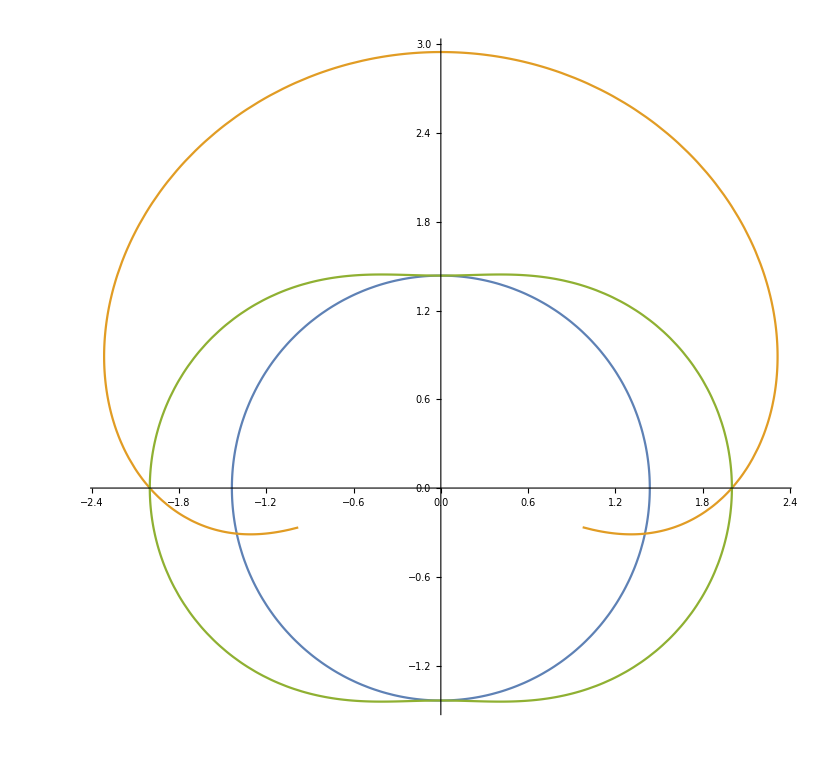

```mathematica
f[z_]:= (a Ω z)/(m  Uz);


a = 0.9;
Ω =4
M=1;
𝒪 = 0.001

Uz=1
PolarPlot[{M+√(M^2-a^2-𝒪^2), M+√(f[Cos[θ-π/2]]+M^2-a^2 Cos[θ-π/2]^2-𝒪^2),  M+√(M^2-𝒪^2-a^2 Cos[θ-π/2]^2)}, {θ,0, 2 π}]
```

```mathematica
Quit[]
```

```mathematica
δ=0
```

0

```mathematica
Simplify[(-(Δ - a^2(1-z^2)))/((r^2+a^2 z^2)^2)(((a^2+r^2) (-δ r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ)+ (a(Ω z+m (a (-1+z^2) ℰ+ℒ)))/m)- a (1-z^2)(r^2+a^2-Δ)/((r^2+a^2 z^2)^2)((Ω z+m (a (-1+z^2) ℰ+ℒ))/(m(1-z^2))+(a (-δ  r+m (a^2+r^2) ℰ-a m ℒ))/(m Δ) )]
```

-ℰ-(a z Ω)/(m r^2+a^2 m z^2)